```mathematica
(*之前最大错误是积分上限错了*)
```

```mathematica
Hq=DiracDelta[x-β-ξ*α]*(Gamma[2*b0+2]*((1-Abs[β])^2-α^2)^b0/(2^(2*b0+1)*(Gamma[b0+1])^2*(1-Abs[β])^(2b0+1)))*Nv*β^(a-1)*(1-β)^b1*(1+c*β^d)/(1-t/λ^2);
```

```mathematica
Hqn=Hq/.{a->0.7,b1->2.03,c->13.8,d->2,Nv->1/2,b0->2,ξ->0.3,λ->0.79,t->-1};
```

```mathematica
a11=Assuming[x>0.3&&x<1,Integrate[Hqn,{β,-1,1},{α,Abs[β]-1,1-Abs[β]}]];
```

```mathematica
a11/.{x->0.5}
```

0.262771-3.69283×10^-14 ⅈ

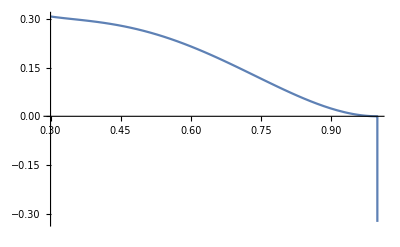

```mathematica
Plot[Re[a11],{x,0.3,1}]
```

```mathematica
1/2*2.6*x^(0.75-1)*(1-x)^0.95
```

```mathematica
Hq2=DiracDelta[x-β-ξ*α]*(Gamma[2*b0+2]*((1-Abs[β])^2-α^2)^b0/(2^(2*b0+1)*(Gamma[b0+1])^2*(1-Abs[β])^(2b0+1)))*1/2*2.6*β^(0.75-1)*(1-β)^0.95/(1-t/λ^2);
```

```mathematica
Hqn2=Hq2/.{b0->2,ξ->0.3,λ->0.79,t->-1};
```

```mathematica
a22=Assuming[x>0.3&&x<1,Integrate[Hqn2,{β,-1,1},{α,Abs[β]-1,1-Abs[β]}]];
```

```mathematica
a22/.{x->0.5}
```

0.323652+6.85915×10^-16 ⅈ

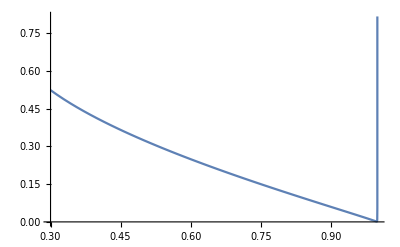

```mathematica
Plot[Re[a22],{x,0.3,1}]
```

```mathematica
(*师兄把δ函数手动替换，计算好像更快，替换注意换了α之后还要除一个ξ*)
```

```mathematica
Hq1=(Gamma[2*b0+2]*((1-Abs[β])^2-α^2)^b0/(2^(2*b0+1)*(Gamma[b0+1])^2*(1-Abs[β])^(2b0+1)))*Nv*β^(a-1)*(1-β)^b1*(1+c*β^d)/(1-t/λ1^2);
```

```mathematica
Hqa=(Hq1/.{α->(x-β)/ξ})/ξ;
Hqan=Hqa/.{a->0.7,b1->2,c->13.8,d->2,Nv->1/2,b0->2,λ1->0.79,t->-1,ξ->0.3,x->0.5};
```

```mathematica
Hqay=Hqa/.{a->0.7,b1->2,c->13.8,d->2,Nv->1/2,b0->2,λ1->0.79,t->-1,ξ->0.3/y,x->0.5/y};
```

```mathematica
NIntegrate[Hqan,{β,2/7,8/13}]
```

0.268058